## Transient response, low-Q

```mathematica
SetDirectory["/home/ybadal/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph 6/Lab 1"]
```

/home/ybadal/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph 6/Lab 1

```mathematica
LoadFile["transient_response_low_q.dat"]
```

transient_response_low_q.dat

File comment header:

Channel 2;   4:29:28 PM 1/16/2018
DAQ: PCI-6221; 16 bits; Max ADC Rate 250kHz, Max ETS 20MHz
Sampling: Eff. Rate 1.25MHz;  ADC Rate 250kHz; Frames 5; Samples 2500
Trigger Delays: Ch1 0.0000S, Ch2 0.0000S; Sweeps averaged: 11
Voltage Offsets: Ch1 0.000V, Ch2 0.000V
Voltage Resolution: Ch1 6.4uV, Ch2 6.4uV
Time (ms)         	Amplitude (V)       	sig Amplitude (V)

Read 2500 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.07,1.635}

n= 1956

544 points removed.

```mathematica
FitData[
 (* The expression defining the function *) A Sin[2 Pi fo t - ϕ Degree]Exp[-t/τ]+c,
(* The symbol for the variable in the expression *) t,
(* A list of the parameters in the function to fit *) {A,fo ,ϕ,τ ,c },
(* A list of starting values for the parameters *) {0.05,15.3,10,0.2,0 }
]
```

n = 1956
p = 5

f[t] = c+A ⅇ^(-t/τ) Sin[2 fo π t-° ϕ]

Fit of (x,y)  (unweighted):

A | = | 0.0776126 | ± | 0.0000102029
fo | = | 15.5638 | ± | 0.000069428
ϕ | = | 17.3716 | ± | 0.00771594
τ | = | 0.359143 | ± | 0.000055592
c | = | 0.00460317 | ± | 1.18338×10^-6Std. Deviation = 0.0000522996

Fit of (x,y±σ_y):

A | = | 0.0776037 | ± | 6.89908×10^-6
fo | = | 15.5638 | ± | 0.0000456056
ϕ | = | 17.3703 | ± | 0.00539098
τ | = | 0.359198 | ± | 0.0000358152
c | = | 0.0046033 | ± | 7.62552×10^-7χ^2/(n - p) = 2.28273

{A→0.0776037,fo→15.5638,ϕ→17.3703,τ→0.359198,c→0.0046033}

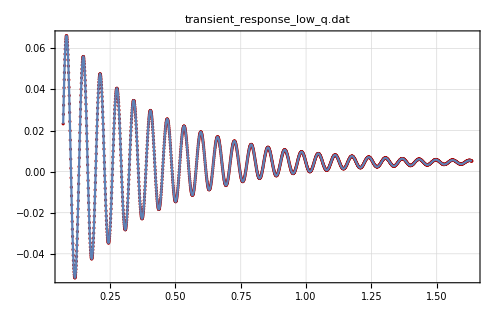
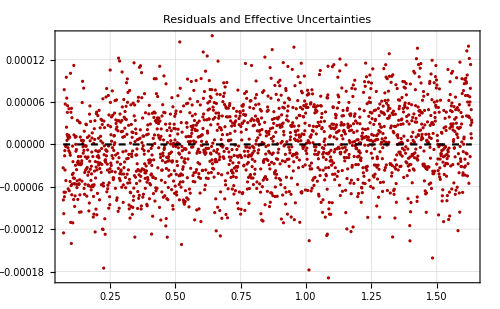
-Graphics-
-Graphics-
f[t] = c+A ⅇ^(-t/τ) Sin[2 fo π t-° ϕ]
          A | = | 0.0776037 | ± | 6.89908×10^-6
fo | = | 15.5638 | ± | 0.0000456056
ϕ | = | 17.3703 | ± | 0.00539098
τ | = | 0.359198 | ± | 0.0000358152
c | = | 0.0046033 | ± | 7.62552×10^-7χ^2/(n - p) = 2.28273

```mathematica
LinearDifferencePlot[Joined->False]
```

## Transient response, high-Q

```mathematica
LoadFile["transient_response_high_q.dat"]
```

transient_response_high_q.dat

File comment header:

Channel 2;   4:36:33 PM 1/16/2018
DAQ: PCI-6221; 16 bits; Max ADC Rate 250kHz, Max ETS 20MHz
Sampling: Eff. Rate 250kHz;  ADC Rate 250kHz; Frames 1; Samples 2500
Trigger Delays: Ch1 0.0000S, Ch2 0.0000S; Sweeps averaged: 11
Voltage Offsets: Ch1 0.000V, Ch2 0.000V
Voltage Resolution: Ch1 6.4uV, Ch2 6.4uV
Time (ms)         	Amplitude (V)       	sig Amplitude (V)

Read 2500 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{0.23,7.625}

n= 1849

651 points removed.

```mathematica
FitData[
 (* The expression defining the function *) A Sin[2 Pi fo t - ϕ Degree]Exp[-t/τ]+c,
(* The symbol for the variable in the expression *) t,
(* A list of the parameters in the function to fit *) {A,fo ,ϕ,τ ,c },
(* A list of starting values for the parameters *) {0.05,15.3,10,2,0 }
]
```

n = 1849
p = 5

f[t] = c+A ⅇ^(-t/τ) Sin[2 fo π t-° ϕ]

Fit of (x,y)  (unweighted):

A | = | 0.0764707 | ± | 6.28735×10^-6
fo | = | 15.5711 | ± | 6.08294×10^-6
ϕ | = | 17.5708 | ± | 0.00472394
τ | = | 2.99424 | ± | 0.00034224
c | = | 0.00478254 | ± | 1.16451×10^-6Std. Deviation = 0.0000500729

Fit of (x,y±σ_y):

A | = | 0.0764802 | ± | 5.60405×10^-6
fo | = | 15.5711 | ± | 4.64279×10^-6
ϕ | = | 17.5691 | ± | 0.00386199
τ | = | 2.99395 | ± | 0.000272138
c | = | 0.00478175 | ± | 8.79915×10^-7χ^2/(n - p) = 1.51638

{A→0.0764802,fo→15.5711,ϕ→17.5691,τ→2.99395,c→0.00478175}

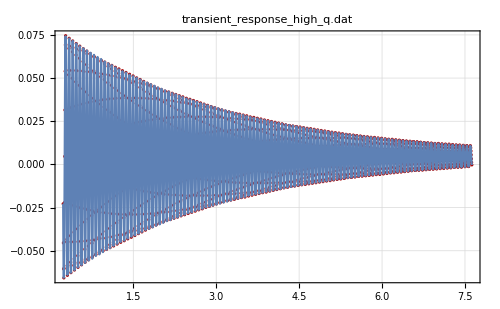
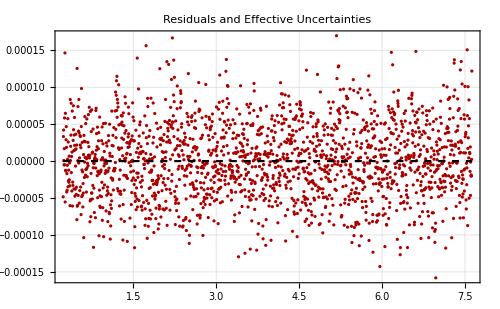
-Graphics-
-Graphics-
f[t] = c+A ⅇ^(-t/τ) Sin[2 fo π t-° ϕ]
          A | = | 0.0764802 | ± | 5.60405×10^-6
fo | = | 15.5711 | ± | 4.64279×10^-6
ϕ | = | 17.5691 | ± | 0.00386199
τ | = | 2.99395 | ± | 0.000272138
c | = | 0.00478175 | ± | 8.79915×10^-7χ^2/(n - p) = 1.51638

```mathematica
LinearDifferencePlot[Joined->False]
```

Analysis

We observe that the transient ring-down qualitatively looks like a decaying sinusoid, as expected. The randomly distributed residuals over a decaying sinusoid fit show that the period of the oscillation is constant.

For the low-Q case, we can calculate:

```mathematica
Subscript[ω, 0]=97922.2;
q=17.593;
Subscript[ω, T]=Subscript[ω, 0] Sqrt[1-1/(4*q^2)]
```

97882.6

```mathematica
%/(2*Pi)
```

15578.5

This corresponds to a frequency of 15578 Hz. The frequency found using the fit parameters is 15564 Hz, which closely agrees. For the high-Q case, we calculate:

```mathematica
Subscript[ω, 0]=97907.99;
q=141.58;
Subscript[ω, T]=Subscript[ω, 0] Sqrt[1-1/(4*q^2)]
```

97907.4

```mathematica
%/(2*Pi)
```

15582.4

This corresponds to a frequency of 155582 Hz. The frequency found using the fit parameters is 155571 Hz, which also agrees.

We can also calculate a predicted value for τ for the low-Q case as follows:

```mathematica
τ=2*q/Subscript[ω, 0]
```

0.000359326

This agrees closely with the 0.00035920 s decay time found using the fit. Similarly, for the high-q case:

```mathematica
τ=2*q/Subscript[ω, 0]
```

0.0028921

This closely agrees with the 0.002993 s decay time found using the fit.